# Bacteria

## 4.

```mathematica
Solve[{βx x+F xin-F/V x-αx x==0,
βy y+F yin-F/V y-c2 x y==0},{x,y}]//FullSimplify
```

{{x→(F V xin)/(F+V αx-V βx),y→(F V yin (F+V (αx-βx)))/(F^2+F V (c2 V xin+αx-βx-βy)+V^2 (-αx+βx) βy)}}

## 5.

```mathematica
Module[{f1,f2,xe,ye,J},
f1[x_,y_]=βx x+F xin-F/V x-αx x;
f2[x_,y_]=βy y+F yin-F/V y-c2 x y;
xe=(F V xin)/(F+V αx-V βx);
ye=(F V yin)/(F+c2 V xe-V βy);
J=Evaluate[({{D[f1[x,y], x], D[f1[x,y], y]}, {D[f2[x,y], x], D[f2[x,y], y]}})]/.{x->xe,y->ye}//MatrixForm]
Module[{f1,f2,xe,ye,J},
f1[x_,y_]=βx x+F xin-F/V x-αx x;
f2[x_,y_]=βy y+F yin-F/V y-c2 x y;
xe=(F V xin)/(F+V αx-V βx);
ye=(F V yin)/(F+c2 V xe-V βy);
J=Evaluate[({{D[f1[x,y], x], D[f1[x,y], y]}, {D[f2[x,y], x], D[f2[x,y], y]}})]/.{x->xe,y->ye};
J.({{x-xe}, {y-ye}})//FullSimplify//MatrixForm]
```

(-F/V-αx+βx | 0
-(c2 F V yin)/(F+(c2 F V^2 xin)/(F+V αx-V βx)-V βy) | -F/V-(c2 F V xin)/(F+V αx-V βx)+βy)

(F (-x/V+xin)+x (-αx+βx)
F (-y/V+yin-(c2 V xin y)/(F+V αx-V βx))+y βy-(c2 F V yin (x-(F V xin)/(F+V αx-V βx)))/(F+(c2 F V^2 xin)/(F+V αx-V βx)-V βy))

## 6.

```mathematica
Module[{f1,f2,xe,ye,J},
f1[x_,y_]=βx x+F xin-F/V x-αx x;
f2[x_,y_]=βy y+F yin-F/V y-c2 x y;
xe=(F V xin)/(F+V αx-V βx);
ye=(F V yin)/(F+c2 V xe-V βy);
J=Evaluate[({{D[f1[x,y], x], D[f1[x,y], y]}, {D[f2[x,y], x], D[f2[x,y], y]}})]/.{x->xe,y->ye};
Eigenvalues[J]//FullSimplify]
```

{-F/V-αx+βx,-F/V-(c2 F V xin)/(F+V αx-V βx)+βy}

## 7.

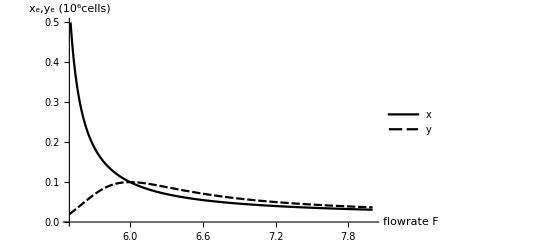

```mathematica
Module[{f1,f2,βx,βy,xin,yin,αx,c2,V,x,y},
βx=0.3;
βy=βx;
V=20;
αx=0.03;
c2=10αx;
xin=0.01/V;
yin=xin;
x[F_]=(F V xin)/(F+V αx-V βx);
y[F_]=(F V yin)/(F+c2 V x[F]-V βy);
Plot[{x[F],y[F]},{F,5.5,8},
PlotRange->{All,{0,.5}},
PlotTheme->"Monochrome",
AxesLabel->{"flowrate F","x_e,y_e (10^6cells)"},
PlotLegends->{"x","y"}]]
```

## 8.

```mathematica
Module[{f1,f2,βx,βy,xin,yin,αx,c2,V,x,y},
βx=0.3;
βy=βx;
V=20;
αx=0.03;
c2=10αx;
xin=0.01/V;
yin=xin;
V(βy-αx)]
```

5.4

# One Predator, Two Preys

## 10.

### b.

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
A[x_,y_,z_,r_]=Evaluate[({{D[f1[x,y,z,r], x], D[f1[x,y,z,r], y], D[f1[x,y,z,r], z]}, {D[f2[x,y,z,r], x], D[f2[x,y,z,r], y], D[f2[x,y,z,r], z]}, {D[f3[x,y,z,r], x], D[f3[x,y,z,r], y], D[f3[x,y,z,r], z]}})];
xe=5/13;
ye=1/13;
ze=8/13;
A[xe,ye,ze,3/2].({{x-xe}, {y-ye}, {z-ze}})//FullSimplify//MatrixForm]
```

(-5/13 (-1+x+z)
1/26 (2-2 y-3 z)
8/13 (-1+2 x+3 y))

```mathematica
Eigenvalues[({{-5/13, 0, -5/13}, {0, -2/26, -3/26}, {2 8/13, 3 8/13, 0}})]//N
```

{-0.14186+0.803369 ⅈ,-0.14186-0.803369 ⅈ,-0.177819}

### c.

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
A[x_,y_,z_,r_]=Evaluate[({{D[f1[x,y,z,r], x], D[f1[x,y,z,r], y], D[f1[x,y,z,r], z]}, {D[f2[x,y,z,r], x], D[f2[x,y,z,r], y], D[f2[x,y,z,r], z]}, {D[f3[x,y,z,r], x], D[f3[x,y,z,r], y], D[f3[x,y,z,r], z]}})];
xe=1;
ye=1;
ze=0;
A[xe,ye,ze,3/2].({{x-xe}, {y-ye}, {z-ze}})//FullSimplify//MatrixForm
]
```

(1-x-z
1-y-(3 z)/2
4 z)

```mathematica
Eigenvalues[({{-1, 0, -1}, {0, -1, -3/2}, {0, 0, 4}})]
```

{4,-1,-1}

## 11.

### a.

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
sys[x_,y_,z_,r_]=
f1[x,y,z,r]==0&&
f2[x,y,z,r]==0&&
f3[x,y,z,r]==0&&
x≥0&&y≥0&&z≥0;
Solve[sys[x,y,z,3],{x,y,z}]]//MatrixForm
```

(x→0 | y→0 | z→0
x→0 | y→1/6 | z→5/18
x→0 | y→1 | z→0
x→1/2 | y→0 | z→1/2
x→1 | y→0 | z→0
x→1 | y→1 | z→0)

### b.

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
A[x_,y_,z_,r_]=Evaluate[({{D[f1[x,y,z,r], x], D[f1[x,y,z,r], y], D[f1[x,y,z,r], z]}, {D[f2[x,y,z,r], x], D[f2[x,y,z,r], y], D[f2[x,y,z,r], z]}, {D[f3[x,y,z,r], x], D[f3[x,y,z,r], y], D[f3[x,y,z,r], z]}})];
xe=1/2;
ye=0;
ze=1/2;
A[xe,ye,ze,r].({{x-xe}, {y-ye}, {z-ze}})//Expand//MatrixForm
]
```

(1/2-x/2-z/2
y-(r y)/2
-1/2+x+r y)

#### x=0

```mathematica
Eigenvalues[({{13/18, 0, 0}, {0, -1/6, -1/2}, {5/9, 5/3, 0}})]//Expand
```

{-1/12+(ⅈ √119)/12,-1/12-(ⅈ √119)/12,13/18}

#### y=0

```mathematica
Eigenvalues[({{-1/2, 0, -1/2}, {0, -1/2, 0}, {1, 3, 0}})]//Expand
```

{-1/4+(ⅈ √7)/4,-1/4-(ⅈ √7)/4,-1/2}

## 13.

### b.

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
sys[x_,y_,z_,r_]=
f1[x,y,z,r]==0&&
f2[x,y,z,r]==0&&
f3[x,y,z,r]==0&&
x==0&&y≥0&&z≥0;
Solve[sys[x,y,z,r],{x,y,z}]]//FullSimplify
```

{{x→0,y→0,z→0},{x→0,y→1,z→0}}

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
A[x_,y_,z_,r_]=Evaluate[({{D[f1[x,y,z,r], x], D[f1[x,y,z,r], y], D[f1[x,y,z,r], z]}, {D[f2[x,y,z,r], x], D[f2[x,y,z,r], y], D[f2[x,y,z,r], z]}, {D[f3[x,y,z,r], x], D[f3[x,y,z,r], y], D[f3[x,y,z,r], z]}})];
xe=0;
ye=1/(2r);
ze=(2r-1)/(2 r^2);
A[xe,ye,ze,r].({{x-xe}, {y-ye}, {z-ze}})//Expand//MatrixForm
]
```

(x+x/(2 r^2)-x/r
1/(2 r)-y/(2 r)-z/2
1/(2 r^2)-1/r-x/r^2+(2 x)/r+2 y-y/r)

```mathematica
Eigenvalues[({{1+1/(2 r^2)-1/r, 0, 0}, {0, -1/(2r), -1/2}, {-1/r^2+2/r, 2-1/r, 0}})]//FullSimplify
```

{1+(1-2 r)/(2 r^2),-(r+√(r^2+8 r^3-16 r^4))/(4 r^2),(-r+√(r^2+8 r^3-16 r^4))/(4 r^2)}

```mathematica
Reduce[r^2-r+1/2>0,r]
```

True

### c.

```mathematica
RowReduce[({{1, 0, 1, 1}, {0, 1, r, 1}, {2, 2r, 0, 1}})]//Simplify//MatrixForm
```

(1 | 0 | 0 | (1-2 r+2 r^2)/(2+2 r^2)
0 | 1 | 0 | (2-r)/(2+2 r^2)
0 | 0 | 1 | (1+2 r)/(2+2 r^2))

```mathematica
Reduce[(1-2 r+2 r^2)/(2+2 r^2)>0&&(2-r)/(2+2 r^2)>0&&(1+2 r)/(2+2 r^2)>0,r]
```

-1/2<r<2

```mathematica
Module[{f1,f2,f3,xe,ye,ze,sys,A},
f1[x_,y_,z_,r_]=x(1-x-z);
f2[x_,y_,z_,r_]=y(1-y-r z);
f3[x_,y_,z_,r_]=z(2x+2 r y-1);
sys[x_,y_,z_,r_]=
f1[x,y,z,r]==0&&
f2[x,y,z,r]==0&&
f3[x,y,z,r]==0&&
x≥0&&y≥0&&z≥0;
Solve[sys[x,y,z,-1/2],{x,y,z}]]//MatrixForm
```

(x→0 | y→0 | z→0
x→0 | y→1 | z→0
x→1/2 | y→0 | z→1/2
x→1 | y→0 | z→0
x→1 | y→1 | z→0)